# HW 2 - ASTR503

## Daniel George - dgeorge5@illinois.edu

## Q1)

## Calculations

### Generating data

```mathematica
Needs["ErrorBarPlots`"];
nQM=N@*QuantityMagnitude;

dx=.5; (*Bin width*)
nP=10^6; (*Number of samples*)
A=dx nP; (*Area under histogram*)

probF=NormalDistribution[10,2];
(*Gaussian distribution*)

dataH=RandomVariate[probF,nP];
(*Random sample from Gaussian*)
```

### Bin counts and errors

```mathematica
binData=Transpose[{Transpose[{MovingAverage[#[[1]],2],#[[2]]/A}],ErrorBar/@(Sqrt[#[[2]]]/A)}&@HistogramList[dataH,{dx}]];
```

### Reduced χ^2 for 10 bins near the peak

```mathematica
chi2R=Total[(PDF[probF]@binData[[#,1,1]]-binData[[#,1,2]])^2/binData[[#,2,1]]^2]/10&[Span@@(Ceiling[Length@binData/2+#]&/@{-4,5})]
```

1.18693

## Plots

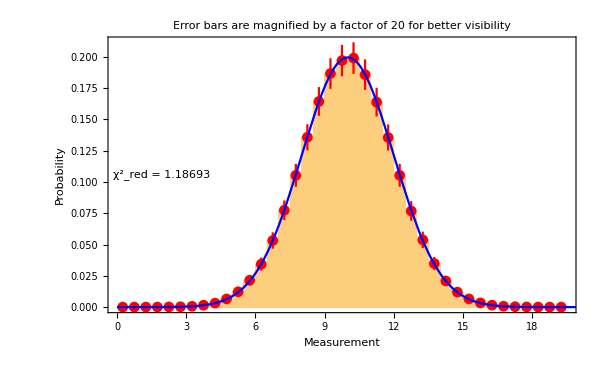

```mathematica
SetOptions[{ListPlot,Histogram,Plot},Frame->True,ImageSize->600,PlotRange->All];Show[Histogram[dataH,{dx},"PDF"],ErrorListPlot[MapAt[20#&,binData,{All,2,1}],PlotStyle->Red,PlotLegends->Placed[PointLegend[{"Measured values"}],{Right,Center}]],Plot[PDF[probF][x] ,{x,0,20},PlotStyle->Blue,PlotLegends->{Placed[LineLegend[{"Actual values"}],{Right,Center}],Placed["  (χ^2)_red = "<>ToString@chi2R,{Left,Center}]}],FrameLabel->{"Measurement","Probability"},PlotLabel->"Error bars are magnified by a factor of 20 for better visibility"]
```

## Q2)

## a)

### Uniformly distributing points inside sphere

```mathematica
nS=10^5; (*Number of supernovae*)
dists=2000Norm/@RandomPoint[Ball[],nS];
```

### Mean distance

```mathematica
Mean@dists Quantity[, "Megaparsecs"]
```

1501.64 Mpc

## b)

### Randomly sampling absolute magnitudes

```mathematica
MList=-19+RandomVariate[NormalDistribution[],nS];
```

### Finding apparent magnitudes

```mathematica
mList=MList+5Log10[dists 10^6/10];
```

### Plot of apparent magnitude vs distance

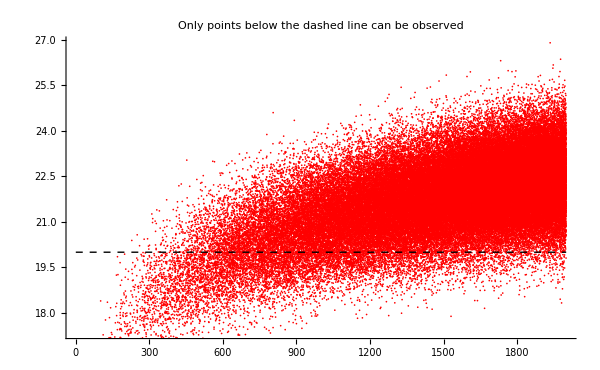

```mathematica
ListPlot[Transpose[{dists,mList}],PlotStyle->{Red,PointSize[.002]},Epilog->{Dashed,Thick,Line[{{0,20},{2000,20}}]},FrameLabel->{"Distance in Mpc","Apparent magnitude"},PlotLabel->"Only points below the dashed line can be observed"]
```

### Selecting observable supernovae

```mathematica
iObs=Flatten@Position[mList,m_/;m≤ 20];
(*Positions in the list for observed supernovae*)
```

### Average apparent magnitudes

#### -- For all samples

```mathematica
Mean@mList
```

21.7797

#### -- For only observed ones

```mathematica
Mean[mList[[iObs]]]
```

19.257

## c)

### Assigning velocities

```mathematica
H0=72.;(*Hubble constant*)
vels=H0*dists; (*True velocities*)
```

### Estimated distances for all supernovae

```mathematica
eDists=10^(1+(mList+19)/5) 10^-6;
```

### Checking that median slope matches correct H_0

```mathematica
Median[vels/eDists]
```

72.0986

### Fit through origin for velocity vs distance

```mathematica
fitH=LinearModelFit[Transpose@{eDists[[iObs]],vels[[iObs]]},{r},r,IncludeConstantBasis->False]
```

FittedModel[137.595 r]

### Velocity vs distance plots

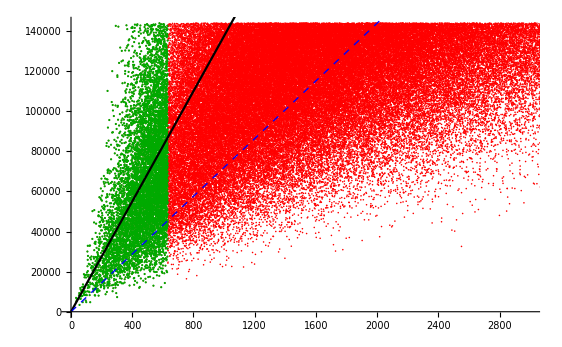

```mathematica
Show[ListPlot[{Transpose[{eDists,vels}],Transpose[{eDists[[iObs]],vels[[iObs]]}]},FrameLabel->{"Distance (Mpc)","Velocity (km/s)"},PlotRange->{{0,3000},{0,Max@vels}},PlotStyle->{{Red,PointSize[.002]},Darker@Green},PlotLegends->Placed[SwatchLegend[{"Estimated distances","Observed distances"}],{Right,Bottom}]],Plot[{fitH[x],H0 x},{x,0,3000},PlotLegends->Placed[LineLegend[{"Observed fit","True values"}],{Right,Bottom}],PlotStyle->{Black,{Dashed,Blue,Thick}}]]
```

We can see that the observed distances are clearly biased. We consistently estimate the distances to be less that the true values. This is because of two reasons: 

1. Although the absolute magnitude (M) is biased equally in both directions, the estimated distance is proportional to 10^M. This causes the estimated distances to be skewed in one direction. 

2. We are unable to observe the supernovae whose magnitudes are shifted to values higher than 20 due to the observing limit. This means we will see more supernovae with absolute magnitudes lower than -19, thus causing us to estimate lower distances.

## d)

### Estimated value of Hubble constant

```mathematica
"H0"-> fitH["BestFitParameters"][[1]]"km/s/Mpc"
```

H0→137.595 km/s/Mpc

The effect of this bias is that it causes us to overestimate the value of the Hubble constant.

### Correcting distance estimates

Since we know that for each velocity there is an equal number of distances above and below the true value, we should use the median of bin counts of distances for each bin of velocity in order to estimate distances.

We should use the above formula to estimate the distance given apparent magnitude. This can be further corrected by first truncating observed samples with high velocities to correct for the finite observing distances.

```mathematica
fitM=LinearModelFit[Log@Median[TransformedDistribution[10.^(1+(#-M)/5) 10^-6,M\[Distributed]NormalDistribution[-19.,1]]]&/@Range[1000],{x},x]
```

FittedModel[-2.7631+0.460517 x]

```mathematica
Mean[TransformedDistribution[10.^(1+(m-x)/5) Mpc,x\[Distributed]NormalDistribution[M,σ]]]
```

10. ⅇ^(0.460517 m-0.460517 M+0.106038 σ^2) Mpc

```mathematica
E^fitM[m]
```

ⅇ^(-2.7631+0.460517 m)

### Fit with corrected distances

```mathematica
vCut=38000;
fitC=LinearModelFit[Select[Transpose@{eDists[[iObs]],vels[[iObs]]},#[[2]]<vCut&],{r},r,IncludeConstantBasis->False]
```

FittedModel[70.6475 r]

### Plot and fit with reduced sample

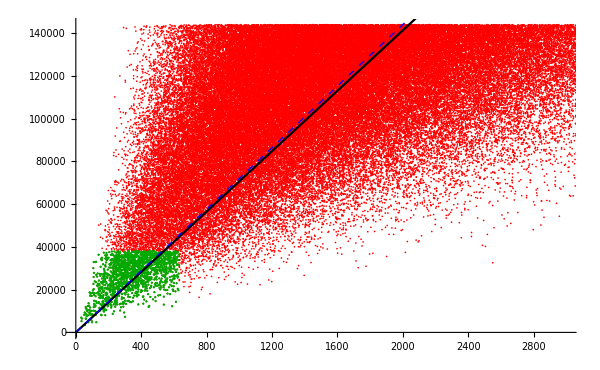

```mathematica
Show[ListPlot[{Transpose[{eDists,vels}],Select[Transpose@{eDists[[iObs]],vels[[iObs]]},#[[2]]<vCut&]},FrameLabel->{"Distance (Mpc)","Velocity (km/s)"},PlotRange->{{0,3000},{0,Max@vels}},PlotStyle->{{Red,PointSize[.002]},Darker@Green},PlotLegends->Placed[SwatchLegend[{"Estimated distances","Selected distances"}],{Right,Bottom}]],Plot[{fitC[x],H0 x},{x,0,3000},PlotLegends->Placed[LineLegend[{"Improved fit","True values"}],{Right,Bottom}],PlotStyle->{Black,{Dashed,Blue,Thick}}]]
```

### Corrected value of H_0 from best fit:

```mathematica
"H0"-> fitC["BestFitParameters"][[1]]"km/s/Mpc"
```

H0→70.6475 km/s/Mpc

### Estimate using median slope for reduced data

```mathematica
"H0"->Median[Divide@@Transpose@Select[Transpose@{vels[[iObs]],eDists[[iObs]]},#[[1]]<vCut/2&]]
```

H0→72.1609

## Q3)

#### Defining constants

```mathematica
k=nQM[Quantity[, "BoltzmannConstant"],"J/K"];h=nQM[Quantity[, "PlanckConstant"],"J/Hz"];
c=nQM[Quantity[, "SpeedOfLight"],"m/s"];
```

## a)

### Defining specific intensity function

```mathematica
i[ν_,T_]:=2h/c^2 ν^3 /(Exp[h ν/(k T)]-1)
```

### Energy density of CMB over the band

```mathematica
uCMB1=UnitConvert[4Pi/c NIntegrate[i[ν,2.73],{ν,824 10^6,894 10^6}]Quantity[, ("Joules")/("Meters")^3],Quantity[, ("Ergs")/("Centimeters")^3]]
```

1.80327×10^-20 ergs/cm^3

## b)

### Photon number density formula

(4 π ∫_ν_min^ν_max (I(ν,T))/(h ν)ⅆν)/c

### Number density over all frequencies

#### For any CMB temperature

```mathematica
4Pi/c Integrate[i[ν,Subscript[T, CMB]]/(h ν),{ν,0,Infinity},Assumptions->Subscript[T, CMB]>0]10^-6/(Quantity[, ("Centimeters")^3]*Quantity[, ("Kelvins")^3])
```

(20.2868 /(cm^3 K^3)) T_CMB^3

#### For given temperature (2.73K)

```mathematica
UnitConvert[4Pi/c Integrate[i[ν,2.73]/(h ν),{ν,0,Infinity}]Quantity[, 1/("Meters")^3],Quantity[, 1/("Centimeters")^3]]
```

412.764 /cm^3

### Number density at T = 2.73K in the given band

```mathematica
UnitConvert[4Pi/c NIntegrate[i[ν,2.73]/(h ν),{ν,824 10^6,894 10^6}]Quantity[, 1/("Meters")^3],Quantity[, 1/("Centimeters")^3]]
```

0.00316646 /cm^3

## c)

### Flux at 1km

Flux is power per unit area. Power is 3 MW.

```mathematica
F1=3.Quantity[, "Megawatts"]/(4 Pi (Quantity[1, "Kilometers"])^2);
```

### Energy density at 1km

Energy density is flux divided by speed of light.

```mathematica
uCP=UnitConvert[F1/Quantity[, "SpeedOfLight"],"erg/cm^3"]
```

7.96326×10^-9 ergs/cm^3

### Ratio to CMB energy density

```mathematica
uCP/uCMB1
```

4.416×10^11

## d)

### Energy density of CMB in new band

```mathematica
uCMB2=UnitConvert[4Pi/c NIntegrate[i[ν,2.73],{ν,161.0 10^9,161.07 10^9}]Quantity[, ("Joules")/("Meters")^3],Quantity[, ("Ergs")/("Centimeters")^3]]
```

1.13194×10^-16 ergs/cm^3

### Ratio to new CMB energy density

```mathematica
uCP/uCMB2
```

7.03507×10^7

### Comparison to previous ratio

This value is smaller than the previous ratio because there is more energy density from the CMB in the second band than the first. This is because the peak of the specific intensity is at about 4000 GHz for T =2.73K as shown in the plot below:

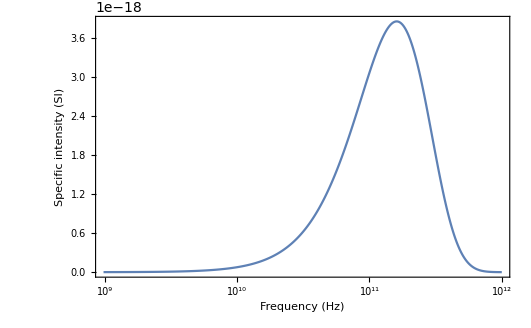

```mathematica
LogLinearPlot[i[v,2.73],{v,0,10^12},PlotRange->All,PlotPoints->1000,Frame->True,FrameLabel->{"Frequency (Hz)","Specific intensity (SI)"}]
```

This peak value can also be obtained using the Wien’s displacement law:

```mathematica
UnitConvert[FormulaData[{"WienDisplacementLaw", "Frequency"},{"T" "Temperature"->Quantity[2.73, "Kelvins"]}][[2]],"Hz"]
```

1.60495×10^11 Hz

## Q4)

## 2)

#### Function to solve for wavelength given energy

```mathematica
fλ[En_]:=NSolve[En==Quantity[, "PlanckConstant"]Quantity[, "SpeedOfLight"] /λ,λ][[1,1]]
```

### a) Ionization energy of Hydrogen

```mathematica
fλ[13.6 Quantity[, "Electronvolts"]]
```

λ→9.11649×10^-8 m

### b) Dissociation energy of Hydrogen

```mathematica
fλ[4.48 Quantity[, "Electronvolts"]]
```

λ→2.7675×10^-7 m

### c) Dissociation energy of CO_2

```mathematica
fλ[11.02 Quantity[, "Electronvolts"]]
```

λ→1.12508×10^-7 m

## 4)

### Finding f_λ /f_ν

Since total energy is conserved:

f_λ dλ  = - f_ν dν

Solving for f_λ /f_ν :

```mathematica
Subscript[f, λ] /Subscript[f, ν] ==With[{ν=c/λ},-Dt[ν]/Dt[λ]]Quantity[, ("Meters")/("Seconds")]//TraditionalForm
```

f_λ/f_ν==(2.99792×10^8 m/s)/λ^2

## 6)

### Photon density

```mathematica
UnitConvert[Quantity[1, "Janskies"]*Quantity[1, "Hertz"]/(Quantity[, "PlanckConstant"]*Quantity[1, "Megahertz"]),"1/(cm^2 s)"]
```

0.00150919 per centimeter^2per second

## 8)

#### Relation between magnitudes and fluxes

```mathematica
eqM:=m1-m2==-2.5Log10[f1/f2]
```

### a) m_b = 8.33

```mathematica
Solve[eqM/.{m1->4.71,f1-> 375,m2-> 8.33},f2][[1,1,2]]Quantity[, "Janskies"]
```

13.3669 Jy

### b) m_b = -0.32

```mathematica
Solve[eqM/.{m1->4.71,f1-> 375,m2-> -.32},f2][[1,1,2]]Quantity[, "Janskies"]
```

38550.6 Jy

## 9)

### Total magnitude formula

```mathematica
mT:=-2.5Log10[10^(-m1 .4)+10^(-m2 .4)]
```

### Substituting values

```mathematica
"Total magnitude" ->  mT/.{m1->8.34,m2->8.34}
```

Total magnitude→7.58743